```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
y[x_]:=1-0.3x+0.04*x^2-4.5*x^3+0.4*x^4+20*RandomReal[{-1,1}];
```

```mathematica
mydata=Table[{x,y[x]},{x,0,10}];

(* Generate the least squares fit *)
(* y(x) = Subscript[a, 0]+Subscript[a, 1] x^2+Subscript[a, 3] x^3+Subscript[a, 4] x^4 *)
(* {1,x,x^2,x^3,x^4} *)
fitdata=Fit[mydata,{1,x,x^2,x^3,x^4},x]
```

7.60093-2.3163 x-0.171044 x^2-4.47619 x^3+0.40069 x^4

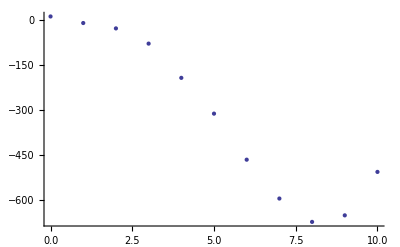

```mathematica
dataplot=ListPlot[mydata]
```

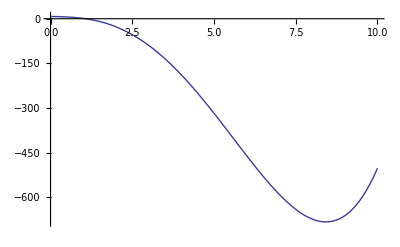

```mathematica
fitplot=Plot[fitdata,{x,0,10}]
```

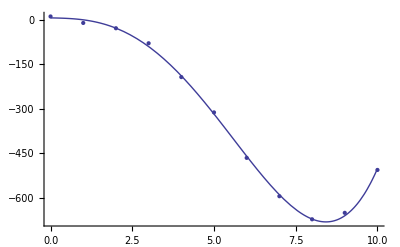

```mathematica
Show[dataplot,fitplot]
```

```mathematica
(* Import data from web *)
webdata=Import["https://eee.uci.edu/12f/40330/lesson3.dat"]
```

{{0.,0.01},{1000.,0.00625},{1800.,0.00476},{2800.,0.0037},{3600.,0.00313},{4400.,0.0027},{5200.,0.00241},{6200.,0.00208}}

```mathematica
newdata=mydata;
newdata[[All,2]]=1/mydata[[All,2]];
```

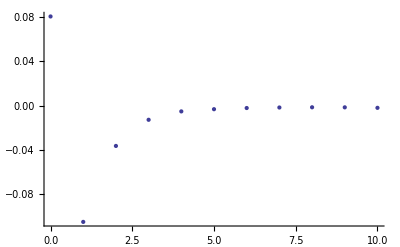

```mathematica
ListPlot[newdata]
```

```mathematica
fitdata=Fit[newdata,{1,x},x]
```

-0.0142344+0.00119385 x

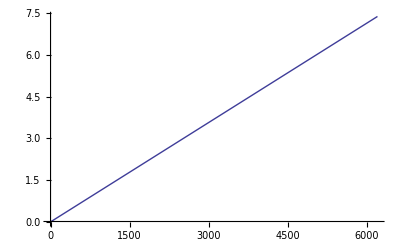

```mathematica
fitplot=Plot[fitdata,{x,0,6200}]
```

```mathematica
(* Statisitics *)
```

```mathematica
data={1.05,1.01,0.97,1.14,0.92,0.99,1.07};
```

```mathematica
Min[data]
```

0.92

```mathematica
Max[data]
```

1.14

```mathematica
Total[data]
```

7.15

```mathematica
Mean[data]
```

1.02143

```mathematica
Median[data]
```

1.01

```mathematica
(* {Subscript[x, i]} *)
```

```mathematica
(* mean: <x>=∑Subscript[x, i]/Subscript[N, i] *)
```

```mathematica
(* variance: σ^2=∑(Subscript[x, i]-<x>)^2/(N-1)*)
```

```mathematica
Variance[data]
```

0.00521429

```mathematica
StandardDeviation[data]
```

0.07221

```mathematica
inputdata=Import["https://eee.uci.edu/12f/40330/lesson4.dat"];
```

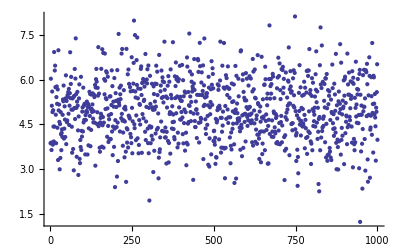

```mathematica
ListPlot[inputdata]
```

```mathematica
data=inputdata[[All,2]];
```

```mathematica
Mean[data]
```

4.98317

```mathematica
StandardDeviation[data]
```

1.01038

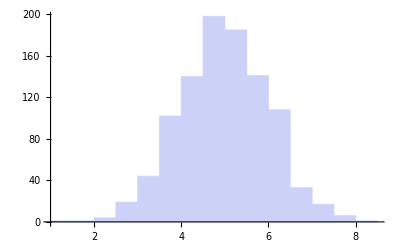

```mathematica
Histogram[data]
```

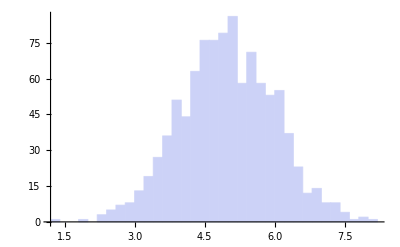

```mathematica
Histogram[data,40]
```

```mathematica
Histogram[data,{0.2}]
```

-Graphics-

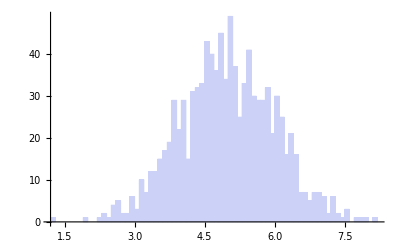

```mathematica
Histogram[data,{0.1}]
```

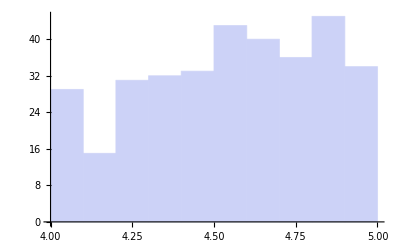

```mathematica
Histogram[data,{4,5,0.1}]
```

```mathematica
(* Prob. density function: P(x) *)
```

```mathematica
(*  Prob. that a value lies btw x and x + dx: P(x)dx*)
```

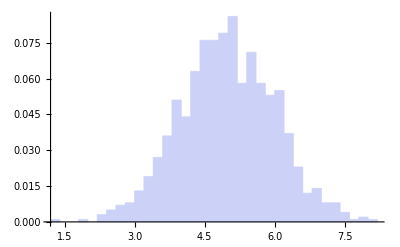

```mathematica
Histogram[data,{0.2},"Probability"]
```

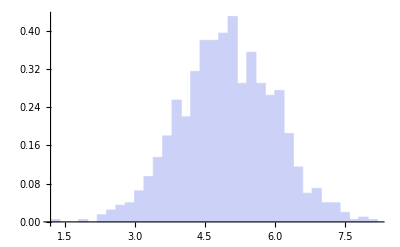

```mathematica
Histogram[data,{0.2},"ProbabilityDensity"]
```

```mathematica
list={a,b,c};
Permutations[list]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

```mathematica
Factorial[3]
```

6

```mathematica
Factorial[0]
```

1

```mathematica
list={a,b,c,d,e};
Permutations[list]
```

{{a,b,c,d,e},{a,b,c,e,d},{a,b,d,c,e},{a,b,d,e,c},{a,b,e,c,d},{a,b,e,d,c},{a,c,b,d,e},{a,c,b,e,d},{a,c,d,b,e},{a,c,d,e,b},{a,c,e,b,d},{a,c,e,d,b},{a,d,b,c,e},{a,d,b,e,c},{a,d,c,b,e},{a,d,c,e,b},{a,d,e,b,c},{a,d,e,c,b},{a,e,b,c,d},{a,e,b,d,c},{a,e,c,b,d},{a,e,c,d,b},{a,e,d,b,c},{a,e,d,c,b},{b,a,c,d,e},{b,a,c,e,d},{b,a,d,c,e},{b,a,d,e,c},{b,a,e,c,d},{b,a,e,d,c},{b,c,a,d,e},{b,c,a,e,d},{b,c,d,a,e},{b,c,d,e,a},{b,c,e,a,d},{b,c,e,d,a},{b,d,a,c,e},{b,d,a,e,c},{b,d,c,a,e},{b,d,c,e,a},{b,d,e,a,c},{b,d,e,c,a},{b,e,a,c,d},{b,e,a,d,c},{b,e,c,a,d},{b,e,c,d,a},{b,e,d,a,c},{b,e,d,c,a},{c,a,b,d,e},{c,a,b,e,d},{c,a,d,b,e},{c,a,d,e,b},{c,a,e,b,d},{c,a,e,d,b},{c,b,a,d,e},{c,b,a,e,d},{c,b,d,a,e},{c,b,d,e,a},{c,b,e,a,d},{c,b,e,d,a},{c,d,a,b,e},{c,d,a,e,b},{c,d,b,a,e},{c,d,b,e,a},{c,d,e,a,b},{c,d,e,b,a},{c,e,a,b,d},{c,e,a,d,b},{c,e,b,a,d},{c,e,b,d,a},{c,e,d,a,b},{c,e,d,b,a},{d,a,b,c,e},{d,a,b,e,c},{d,a,c,b,e},{d,a,c,e,b},{d,a,e,b,c},{d,a,e,c,b},{d,b,a,c,e},{d,b,a,e,c},{d,b,c,a,e},{d,b,c,e,a},{d,b,e,a,c},{d,b,e,c,a},{d,c,a,b,e},{d,c,a,e,b},{d,c,b,a,e},{d,c,b,e,a},{d,c,e,a,b},{d,c,e,b,a},{d,e,a,b,c},{d,e,a,c,b},{d,e,b,a,c},{d,e,b,c,a},{d,e,c,a,b},{d,e,c,b,a},{e,a,b,c,d},{e,a,b,d,c},{e,a,c,b,d},{e,a,c,d,b},{e,a,d,b,c},{e,a,d,c,b},{e,b,a,c,d},{e,b,a,d,c},{e,b,c,a,d},{e,b,c,d,a},{e,b,d,a,c},{e,b,d,c,a},{e,c,a,b,d},{e,c,a,d,b},{e,c,b,a,d},{e,c,b,d,a},{e,c,d,a,b},{e,c,d,b,a},{e,d,a,b,c},{e,d,a,c,b},{e,d,b,a,c},{e,d,b,c,a},{e,d,c,a,b},{e,d,c,b,a}}

```mathematica
Length[Permutations[list]]
```

120

```mathematica
Factorial[5]
```

120

```mathematica
(* list of n elems *)
```

```mathematica
(* Divided into m elems and n-m elems *)
```

```mathematica
(* #ways, w/o regard for order: n!/(n-m)! * (n-m)!/(m!*(n-m)!)n!/(m!(n-m)!) *)
```

```mathematica
(* Binomial coef. *)
```

```mathematica
(* #ways to make n-m: n(n-1)(n-2)...(n-m+1)(n-m) *)
```

```mathematica
(* =n!/(n-m)! *)
```

```mathematica
(* #ways to make m: (n-m)! *)
```

```mathematica
Binomial[4,3]
```

4